```mathematica
wiL[f_, a_,b_, c_]:=Module[
{
 z,
j= a,
dx=CreateDataStructure["DynamicArray"],
dy=CreateDataStructure["DynamicArray"],
w=0,
cd
},
z= Sqrt[Power[b-a,2]]/(c - 1);
For[k = 1, k<=c,++k,
dx["Append",j];
dy["Append",N[f[j]]];
j +=z;
];

For[i=1,i<=dx["Length"],i++,
cd=1;
For[k=1,k<i,k++,
cd=cd*(x-dx["Part",k])/(dx["Part",i]-dx["Part",k]);
];
For[k=i+1,k<=dx["Length"],k++,
cd=cd*(x-dx["Part",k])/(dx["Part",i]-dx["Part",k]);
];
w=w+dy["Part",i]*cd;
];

Return[FullSimplify[w]];
]
```

```mathematica
f[x_]:=(x-Sin[2 x]) Cos[2 x]-E^-x;
```

```mathematica
wiL[f,-2,3,6]
```

-1.+x (1.57625+x (-0.493925+x (-0.529739+(-0.0491561+0.0909473 x) x)))

```mathematica
p1 =Plot[f[x],{x,-2,3},PlotStyle->Green]
```

```mathematica
p2 =Plot[wiL[f,-2,3,6],{Plot[x,-2,3]}, PlotStyle->{Dashed,Red}]
```

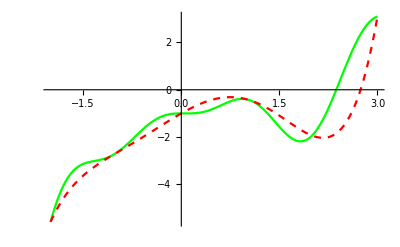

```mathematica
Show[p1,p2]
```

```mathematica
wiL[f,-2,3,15]
```

-1.00008+x (0.000232051+x (-0.497011+x (3.49696+x (-0.0592738+x (-3.58005+x (0.0364206+x (1.51599+x (-0.0378458+x (-0.334829+x (0.0189442+x (0.0415645+x (-0.00456151+(-0.0023595+0.000416047 x) x))))))))))))

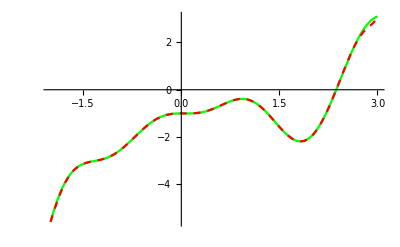

```mathematica
p3 =Plot[wiL[f,-2,3,15],{x,-2,3}, PlotStyle->{Dashed,Red}]
Show[p1,p3]
```

```mathematica
wiL[f,-2,3,20]
```

-1.+x (-7.30312×10^-7+x (-0.500009+x (3.50003+x (-0.041594+x (-3.59187+x (-0.00156523+x (1.53734+x (0.0000429804+x (-0.35575+x (0.00024597+x (0.0528902+x (-0.000341441+x (-0.00558221+x (0.000178754+x (0.000422863+x (-0.0000419712+x (-0.0000168975+(3.66629×10^-6-1.9398×10^-7 x) x)))))))))))))))))

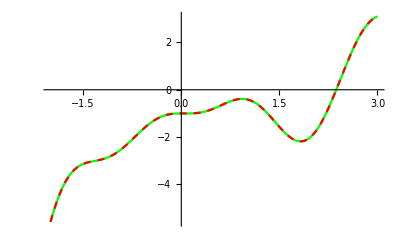

```mathematica
p4 =Plot[wiL[f,-2,3,20],{x,-2,3}, PlotStyle->{Dashed,Red}]
Show[p1,p4]
```